### Model epidemije (SIR)

Poln sistem enačb

```mathematica
f={a BB DD - b BB,-a BB DD + g II, -g II + b BB}
```

{-b BB+a BB DD,-a BB DD+g II,b BB-g II}

Zastojne točke

```mathematica
sol=Solve[Flatten[{Thread[f==0],BB+DD+II==N0}],{BB,DD,II}]
```

{{BB→0,DD→N0,II→0},{BB→(g (-b+a N0))/(a (b+g)),DD→b/a,II→-(b (b-a N0))/(a (b+g))}}

Jakobijan

```mathematica
jac=Grad[f,{BB,DD,II}];
jac//MatrixForm
```

(-b+a DD | a BB | 0
-a DD | -a BB | g
b | 0 | -g)

```mathematica
MatrixForm/@(jac/.sol)
```

{(-b+a N0 | 0 | 0
-a N0 | 0 | g
b | 0 | -g),(0 | (g (-b+a N0))/(b+g) | 0
-b | -(g (-b+a N0))/(b+g) | g
b | 0 | -g)}

Reduciran problem na 2D z ohranitvijo populacije

```mathematica
ff=Most[f/.II->N0-DD-BB]
```

{-b BB+a BB DD,-a BB DD+g (-BB-DD+N0)}

Zastojne točke

```mathematica
sol=Solve[Thread[ff==0],{BB,DD}]
```

{{BB→0,DD→N0},{BB→(g (-b+a N0))/(a (b+g)),DD→b/a}}

Jakobijan

```mathematica
jac=Grad[ff,{BB,DD}];
jac//MatrixForm
```

(-b+a DD | a BB
-a DD-g | -a BB-g)

```mathematica
MatrixForm/@(jac/.sol)
```

{(-b+a N0 | 0
-g-a N0 | -g),(0 | (g (-b+a N0))/(b+g)
-b-g | -g-(g (-b+a N0))/(b+g))}

Bolna in dovzetna populacija v zastojni točki

```mathematica
BB+DD/.sol//Simplify
```

{N0,(b^2+a g N0)/(a b+a g)}

```mathematica
Manipulate[Module[{tempfunction,gp,gg,sp,os,nsl},
tempfunction:=ff/.{N0->1,a->aaa,b->bbb,g->ggg};
nsl={BB[t],DD[t]}/.NDSolve[{BB'[t]==-bbb BB[t]+aaa BB[t]DD[t],DD'[t]==-aaa BB[t]DD[t]+ggg(1-DD[t]-BB[t]),DD[0]==0.99,BB[0]==0.01},{BB[t],DD[t]},{t,0,tmax}][[1]];
gp=ListPlot[({BB,DD}/.sol)/.{N0->1,a->aaa,b->bbb,g->ggg}];
gg=Graphics[{Black,Opacity[0.5],Polygon[{{1,1},{1,0},{0,1}}]}];
sp=StreamPlot[tempfunction,{BB,0,1},{DD,0,1},FrameLabel->{"Bolni","Dovzetni"}, ImageSize->Large];
os=ParametricPlot[nsl,{t,0,tmax},PlotStyle->Black];
GraphicsColumn[{Show[sp,gp,gg,os],
Plot[nsl,{t,0,tmax},PlotRange->{0,1},PlotLabels->{"Bolni","Dovzetni"}]}]
]
,{{aaa,1},0.01,2},{{bbb,0.5},0,2},{{ggg,0},0,1},{{tmax,100},0,1000}]
```

### Zajci

```mathematica
fzajci={α Z-β L Z,-γ L + δ L Z};
Manipulate[Module[{tempfunction,dsolution},
tempfunction:=fzajci/.{α->aaa,β->bbb,γ->ggg,δ->ddd};
dsolution={z[t],l[t]}/.NDSolve[{z'[t]==aaa z[t]-bbb l[t]z[t],l'[t]==-ggg l[t]+ddd l[t]z[t],z[0]==1,l[0]==0.5},{z[t],l[t]},{t,0,10}][[1]];
GraphicsColumn[{
Show[StreamPlot[tempfunction,{Z,0,3},{L,0,3},FrameLabel->{"Zajci","Lisice"}, ImageSize->Large],
ParametricPlot[dsolution,{t,0,10},PlotStyle->Black]
],
Plot[dsolution,{t,0,10},PlotLabels->{"Zajci","Lisice"},PlotRange->{Automatic,{0,All}}]
}]
]
,{{aaa,1},0.1,2},{{bbb,1},0.1,2},{{ggg,1},0.1,2},{{ddd,1},0.1,2}]
```

### Dušeno nitno nihalo

```mathematica
funkcija={v,-β v-k Sin[x]};
Manipulate[Module[{tempfunction,jacc,cp,sp},
tempfunction:=funkcija/.{β->ββ,k->kk};
jacc=Grad[funkcija,{x,v}]/.{x->0,v->0,β->ββ,k->kk};
cp=ComplexListPlot[Eigenvalues[jacc],PlotRange->{{-1.2,1.2},{-1.2,1.2}},PlotStyle->PointSize[Large]];
sp=StreamPlot[tempfunction,{x,-2π,2π},{v,-2,2},FrameLabel->{"x","v"}, ImageSize->Large];
GraphicsGrid[{{sp,cp}}]
]
,{{ββ,0},0,2},{{kk,1},0,1}]
```

### Kvadratno dušeno nihalo

```mathematica
funkcija={v,-β Abs[v]v-k x};
Manipulate[Module[{tempfunction,sp},
tempfunction:=funkcija/.{β->ββ,k->kk};
sp=StreamPlot[tempfunction,{x,-2.5π,2.5π},{v,-2,2},FrameLabel->{"x","v"}, ImageSize->Large]
]
,{{ββ,0},0,2},{{kk,1},0,1}]
```

Prvi integral (konstanta gibanja na pol - ravnini)

```mathematica
w[x_,a_,β_]=a ⅇ^(-2 x β)+k/(4 β^2)-(k x)/(2 β)/.k->1
```

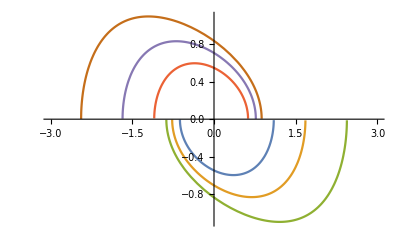

```mathematica
Plot[{-Sqrt[w[x,-0.7,-0.5]],-Sqrt[w[x,-0.5,-0.5]],-Sqrt[w[x,-0.3,-0.5]],Sqrt[w[x,-0.7,0.5]],Sqrt[w[x,-0.5,0.5]],Sqrt[w[x,-0.3,0.5]]},{x,-3,3}]
```

### Laserski sistem

Osnovni sistem

```mathematica
funlaser={-alfa F + gama  a F,-beta a - delta a F + R}
```

{-alfa F+a F gama,-a beta-a delta F+R}

```mathematica
resitev=Solve[Thread[funlaser=={0,0}],{a,F}]
```

{{a→alfa/gama,F→(-alfa beta+gama R)/(alfa delta)},{a→R/beta,F→0}}

Brezdimenzijska oblika

```mathematica
funlaser={-alfa (F -   a F),-beta (a + a F-r)}
```

{-alfa (F-a F),-beta (a+a F-r)}

Lepša oblika stacionarnih točk

```mathematica
resitev=Solve[Thread[funlaser=={0,0}],{a,F}]
```

{{a→1,F→-1+r},{a→r,F→0}}

Jakobijan

```mathematica
jac=Grad[funlaser,{F,a}]/.{a->1,F->r-1}//Simplify;
jac//MatrixForm
```

(0 | alfa (-1+r)
-beta | -beta r)

```mathematica
charpol=CharacteristicPolynomial[jac,λ]
```

-alfa beta+alfa beta r+beta r λ+λ^2

```mathematica
Q=Sqrt[Coefficient[charpol,λ,0]]/Coefficient[charpol,λ,1]//Simplify
```

(√(alfa beta (-1+r)))/(beta r)

```mathematica
Manipulate[Module[{tempfunction,nsl},
tempfunction:=funlaser/.{alfa->α,beta->β,r->rr};
nsl={F[t],a[t]}/.NDSolve[{F'[t]==-α (F[t] -   a[t] F[t]),a'[t]==-β (a[t] + a[t] F[t]-rr),a[0]==0.0,F[0]==0.1},{F[t],a[t]},{t,0,tmax}][[1]];
GraphicsColumn[{
Show[StreamPlot[tempfunction,{F,0,2},{a,0,2},FrameLabel->{"f","a"}, ImageSize->Large],ParametricPlot[nsl,{t,0,tmax},PlotStyle->Black]],
Plot[nsl,{t,0,tmax},PlotRange->All]
}
]
]
,{{α,1},0,2},{{β,1},0,2},{{rr,1.5},0,3},{{tmax,100},0,420}]
```